# ChiSquared

```mathematica
dist=ChiSquareDistribution[k]
```

ChiSquareDistribution[k]

```mathematica
PDF[dist,z]
```

Piecewise[{{(2^(-k/2) ⅇ^(-z/2) z^(-1+k/2))/Gamma[k/2], z>0}, {0, True}}]

```mathematica
CDF[dist,z]
```

Piecewise[{{GammaRegularized[k/2,0,z/2], z>0}, {0, True}}]

```mathematica
Manipulate[Plot[PDF[ChiSquareDistribution[k],x],{x,0,6},Filling->Axis],{k,0.5,5}]
```

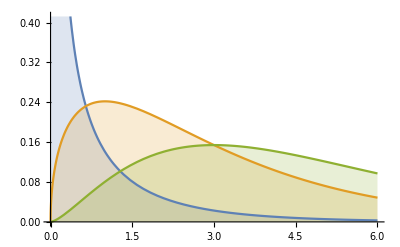

```mathematica
Plot[Table[PDF[ChiSquareDistribution[ν],x],{ν,{0.5,3,5}}]//Evaluate,{x,0,6},Filling->Axis]
```

```mathematica
Mean[dist]
```

k

```mathematica
Median[dist]
```

2 InverseGammaRegularized[k/2,0,1/2]

```mathematica
Variance[dist]
```

2 k

```mathematica
StandardDeviation[dist]
```

√2 √k

```mathematica
Skewness[dist]
```

2 √2 √(1/k)

```mathematica
Kurtosis[dist]
```

3+12/k

```mathematica
CharacteristicFunction[dist,t]
```

(1-2 ⅈ t)^(-k/2)

```mathematica
Random[ChiSquareDistribution[1]]
```

1.38853